```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
Needs["SSSiCv100`"];
```

### New code: EDSL-To-Trana-Notation

```mathematica
EDSLToTrana[{IndexedConcatenate[x__,iter0_]}]:=Module[{argList=List[x],basedArgList,k,kmax,iter,base},
iter=
Which[
AtomQ[iter0],{n,0,iter0-1},
Length[iter0]==2, {First[iter0],1,Last[iter0]},
True,iter0
];
If[$debug,Print["iter: ",iter]];
kmax= Length[argList];
If[$debug,Print["kmax: ",kmax]];
basedArgList=MapIndexed[{Expand[kmax * (iter[[1]]-iter[[2]])]+First[#2],#1}&,argList,{1}];
If[$debug,Print["argList: ",argList]];
If[$debug,Print["basedArgList: ",basedArgList]];
{IndexedConcatenate[
Sequence@@Flatten[
Replace[basedArgList, {base_,eds_List}:>(Rule[base,base+#]&/@eds),{1}]
],
iter]}
]
```

### Try it on ICN Paper Examples

#### Figure 5a

```mathematica
IC2a={IndexedConcatenate[{1},10]}
```

{€^10[{1}]}

```mathematica
EDSLToTrana[IC2a]
```

{€_(n⊨0)^9[1+n→2+n]}

```mathematica
Expand[%]
```

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→11}

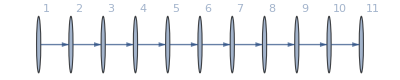

```mathematica
Graph[%,VertexLabels->Automatic]
```

```mathematica
{$debug=True,EDSLToTrana[IC2a],$debug=False}[[2]]
```

iter: {n,0,9}

kmax: 1

argList: {{1}}

basedArgList: {{1+n,{1}}}

{€_(n⊨0)^9[1+n→2+n]}

```mathematica
IC2a={IndexedConcatenate[{1},{n,1,10}]}
```

{€_(n⊨1)^10[{1}]}

```mathematica
EDSLToTrana[IC2a]
```

{€_(n⊨1)^10[n→1+n]}

```mathematica
Expand[%]
```

{1→2,2→3,3→4,4→5,5→6,6→7,7→8,8→9,9→10,10→11}

```mathematica
Graph[%,VertexLabels->Automatic]
```

-Graphics-

```mathematica
{$debug=True,EDSLToTrana[IC2a],$debug=False}[[2]]
```

iter: {n,1,10}

kmax: 1

argList: {{1}}

basedArgList: {{n,{1}}}

{€_(n⊨1)^10[n→1+n]}

#### Figure 5b

```mathematica
IC2b={IndexedConcatenate[{1},{},{n,1,5}]}
```

{€_(n⊨1)^5[{1},{}]}

```mathematica
EDSLToTrana[IC2b]
```

{€_(n⊨1)^5[2 n-1→2 n]}

```mathematica
Expand[%]
```

{1→2,3→4,5→6,7→8,9→10}

```mathematica
Graph[%,VertexLabels->Automatic]
```

-Graphics-

```mathematica
{$debug=True,EDSLToTrana[IC2b],$debug=False}[[2]]
```

iter: {n,1,5}

kmax: 2

argList: {{1},{}}

basedArgList: {{-1+2 n,{1}},{2 n,{}}}

{€_(n⊨1)^5[2 n-1→2 n]}

#### Figure 5c

```mathematica
IC2c={IndexedConcatenate[{1,2},{n,1,10}]}
```

{€_(n⊨1)^10[{1,2}]}

```mathematica
EDSLToTrana[%]
```

{€_(n⊨1)^10[n→n+1,n→n+2]}

```mathematica
Expand[%]
```

{1→2,1→3,2→3,2→4,3→4,3→5,4→5,4→6,5→6,5→7,6→7,6→8,7→8,7→9,8→9,8→10,9→10,9→11,10→11,10→12}

```mathematica
Graph[%,VertexLabels->Automatic]
```

-Graphics-

```mathematica
{$debug=True,EDSLToTrana[IC2c],$debug=False}[[2]]
```

iter: {n,1,10}

kmax: 1

argList: {{1,2}}

basedArgList: {{n,{1,2}}}

{€_(n⊨1)^10[n→n+1,n→n+2]}

#### Figure 6d

```mathematica
IC2d={IndexedConcatenate[{2,3},{3},{1,2},{m,1,9}]}
```

{€_(m⊨1)^9[{2,3},{3},{1,2}]}

```mathematica
EDSLToTrana[%]
```

{€_(m⊨1)^9[3 m-2→3 m,3 m-2→3 m+1,3 m-1→3 m+2,3 m→3 m+1,3 m→3 m+2]}

```mathematica
Expand[%]
```

{1→3,1→4,2→5,3→4,3→5,4→6,4→7,5→8,6→7,6→8,7→9,7→10,8→11,9→10,9→11,10→12,10→13,11→14,12→13,12→14,13→15,13→16,14→17,15→16,15→17,16→18,16→19,17→20,18→19,18→20,19→21,19→22,20→23,21→22,21→23,22→24,22→25,23→26,24→25,24→26,25→27,25→28,26→29,27→28,27→29}

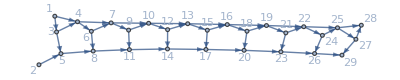

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

#### Figure 5e

EDSL representations:

```mathematica
ICNB11={IndexedConcatenate[IndexedConcatenate[{2j-1, 2j}, {j, 1, 3}], IndexedConcatenate[{1, 2}, IndexedConcatenate[{}, 2], 2], 3]};
ICNB10={IndexedConcatenate[IndexedConcatenate[{2j+1, 2j+2}, {j,0,2}], IndexedConcatenate[{1, 2}, IndexedConcatenate[{}, {k,0,1}],{j,0,1}],{i,0,2}]};
Row[{ICNB11,ICNB10,Style[Column[Partition[Expand[ICNB1],9]],Small]}," = "]
```

=  = {€^3[€_(j⊨1)^3[{2 j-1,2 j}],€^2[{1,2},€^2[{}]]]}{€_(i⊨0)^2[€_(j⊨0)^2[{2 j+1,2 j+2}],€_(j⊨0)^1[{1,2},€_(k⊨0)^1[{}]]]}{{1,2},{3,4},{5,6},{1,2},{},{},{1,2},{},{}}
{{1,2},{3,4},{5,6},{1,2},{},{},{1,2},{},{}}
{{1,2},{3,4},{5,6},{1,2},{},{},{1,2},{},{}}

There are 9 edge difference sets in each row of the EDSL — for each “i” in the outer I-Cat, but they describe 10 edges, given below:

```mathematica
Grid[Riffle[#,","]& /@ Partition[FromNetDifferenceSets[ExpandAll[ICNB11]],10]]
```

1→2 | , | 1→3 | , | 2→5 | , | 2→6 | , | 3→8 | , | 3→9 | , | 4→5 | , | 4→6 | , | 7→8 | , | 7→9
10→11 | , | 10→12 | , | 11→14 | , | 11→15 | , | 12→17 | , | 12→18 | , | 13→14 | , | 13→15 | , | 16→17 | , | 16→18
19→20 | , | 19→21 | , | 20→23 | , | 20→24 | , | 21→26 | , | 21→27 | , | 22→23 | , | 22→24 | , | 25→26 | , | 25→27

The 9 comes from adding up the lengths of the internal ICs, which represent 3×1 + 2×(1+2×1)=3+2×3=3+6=9 elements

There is only 1 edge difference set inside the first “j” I-Cat, and 3 inside the second. In the following, 
(9i+j) comes from the 9 EDSs in the outer I-Cat and the 1 in the first “j” I-Cat;
(9i+3+3j) ”      ”        ”   9 EDSs  ”     ”       ”          ” ,   the 3 in order to to pass the first “j” I-Cat entirely, the 3j comes from the 3 EDSs in the 2nd “j” I-Cat. 
The final integer before each “→” is the vertex number in the inner I-Cat: 1.
The parenthesized expressions at the end of each “→” expression come from the EDSL internal expressions, when 0-indexed (2nd form shown above).

```mathematica
ICNB1Trana=
{IndexedConcatenate[
IndexedConcatenate[(9i+j)+1->(9i+j)+1+(2j+1),(9i+j)+1->(9i+j)+1+(2j+2),{j,0,2}],
IndexedConcatenate[(9i+3+3j)+1->(9i+3+3j)+1+(1),(9i+3+3j)+1->(9i+3+3j)+1+(2),{j,0,1}],
{i,0,2}
]}
```

{€_(i⊨0)^2[€_(j⊨0)^2[1+9 i+j→2+9 i+3 j,1+9 i+j→3+9 i+3 j],€_(j⊨0)^1[4+9 i+3 j→5+9 i+3 j,4+9 i+3 j→6+9 i+3 j]]}

{€_(i⊨0)^2[€_(j⊨0)^2[(9i+j)+1->(9i+j)+1+(2j+1),(9i+j)+1->(9i+j)+1+(2j+2),],€_(j⊨0)^1[(9i+3+3j)+1->(9i+3+3j)+1+(1),(9i+3+3j)+1->(9i+3+3j)+1+(2)]]}

```mathematica
ExpandAll[ICNB1Trana]
```

{1→2,1→3,2→5,2→6,3→8,3→9,4→5,4→6,7→8,7→9,10→11,10→12,11→14,11→15,12→17,12→18,13→14,13→15,16→17,16→18,19→20,19→21,20→23,20→24,21→26,21→27,22→23,22→24,25→26,25→27}

```mathematica
FromNetDifferenceSets@ExpandAll[ICNB11]
```

{1→2,1→3,2→5,2→6,3→8,3→9,4→5,4→6,7→8,7→9,10→11,10→12,11→14,11→15,12→17,12→18,13→14,13→15,16→17,16→18,19→20,19→21,20→23,20→24,21→26,21→27,22→23,22→24,25→26,25→27}

```mathematica
%133==%134
```

True

```mathematica
Expand[%]
```

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

#### Figure 5f

```mathematica
ICNB2={IndexedConcatenate[{2,2,2},{1,3,3},{2},{1,1,3},{2},{1,1,1},{3},4]}
```

```mathematica
EDSLToTrana[%]
```

```mathematica
Expand[%]
```

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

#### Figure 5g

```mathematica
ICNB3={IndexedConcatenate[{2, 3}, {1, 2}, {}, 8]}
```

```mathematica
EDSLToTrana[%]
```

```mathematica
Expand[%]
```

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

#### Figure 5h

```mathematica
ICNB4={IndexedConcatenate[{1, 6, 8}, {}, {IndexedConcatenate[2,4]}, IndexedConcatenate[{1, IndexedConcatenate[3,3]}, {}, 2], 7]}
```

```mathematica
EDSLToTrana[%]
```

```mathematica
Expand[%]
```

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

#### Figure 5i

```mathematica
ICB5={IndexedConcatenate[IndexedConcatenate[{1,18-2k},{k,1,7}],IndexedConcatenate[{1,1},{k,8,9}],{n,0,25}]}
```

```mathematica
EDSLToTrana[%]
```

```mathematica
Expand[%]
```

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

#### Figure 5j

```mathematica
ICB6={IndexedConcatenate[IndexedConcatenate[{1,7,8},2],IndexedConcatenate[{1,1,7},2],{7},{},{},13]}
```

```mathematica
EDSLToTrana[%]
```

```mathematica
Expand[%]
```

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

#### Figure 5k

```mathematica
ICB5b={IndexedConcatenate[IndexedConcatenate[{1,12-2k},{k,1,4}],IndexedConcatenate[{1,1},{k,5,7}],{n,0,18}]}
```

```mathematica
EDSLToTrana[%]
```

```mathematica
Expand[%]
```

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

#### Figure 6a

```mathematica
IC2D1={IndexedConcatenate[{1,1,1},{1,1,1+i},IndexedConcatenate[{1,1,2+i},-1+i],{2+i,3+i},{i,1,10}]}
```

```mathematica
EDSLToTrana[%]
```

```mathematica
Expand[%]
```

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

#### Figure 6b

```mathematica
IC2D2={IndexedConcatenate[{-1+2 k,1+2 k},IndexedConcatenate[{1,1},{1,2 k},k],{k,1,12}]}
```

```mathematica
EDSLToTrana[%]
```

```mathematica
Expand[%]
```

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

#### Figure 6c

```mathematica
IC2D4={IndexedConcatenate[IndexedConcatenate[{},{1,1,2,2k},k-1],{},{2k,2(1+k)},{k,1,8}]}
```

```mathematica
EDSLToTrana[%]
```

```mathematica
Expand[%]
```

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

#### Figure 6d

```mathematica
IC3D1={IndexedConcatenate[IndexedConcatenate[IndexedConcatenate[HoldForm@{z=n(n+1)/2,z+i,z+i+1},i],{i,1,n}],{n,1,5}]}
```

```mathematica
EDSLToTrana[%]
```

```mathematica
Expand[%]
```

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

#### Figure 6e

```mathematica
IC2c={IndexedConcatenate[IndexedConcatenate[{k,k+1},k],{k,1,9}]}
```

```mathematica
EDSLToTrana[%]
```

```mathematica
Expand[%]
```

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```

#### Figure 6f

```mathematica
IC2j={IndexedConcatenate[{-1 + 2^k, 2^k, 1 + 2^k}, IndexedConcatenate[{1 + 2^k}, 1 + 2^k], {1}, 
 IndexedConcatenate[{1, -1 + 2^k + j, 2^k + j}, {j, 1, -1 + 2^k}], {k, 1, 10}]}
```

```mathematica
EDSLToTrana[%]
```

```mathematica
Expand[%]
```

```mathematica
Graph[%,VertexLabels->Automatic,GraphLayout->"SpringElectricalEmbedding"]
```